```mathematica
eq=ϕ''[y]==-p0/e+(ϕ[y])/ld^2;
psol=DSolve[{eq,ϕ'[0]==-σ/e,ϕ'[L]==σ/e},ϕ[y],y];
pf[y_]=FullSimplify[Expand[psol[[1,1,2]]]]
```

(ld (ld p0+σ Cosh[(L-2 y)/(2 ld)] Csch[L/(2 ld)]))/e

```mathematica
eqf=-η v''[y] ==
```

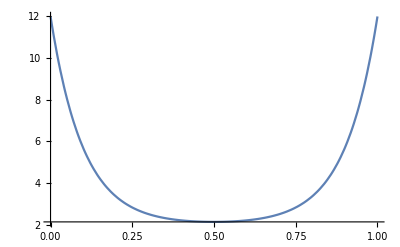

```mathematica
Plot[f[y],{y,0,1}]
```